```mathematica
path=NotebookDirectory[];
SetDirectory[path];
tfifilenames=FileNames["*.tfi"];
tffiles=path<>#&/@tfifilenames;
```

```mathematica
ReadTF[tf_]:=Module[{rgba},
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
alpha=(#/255.&)/@a;
rgba=(#/255.&)/@Transpose[{r,g,b,a}];
rgba[[2;;-2]]]
```

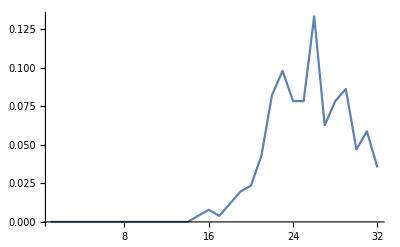
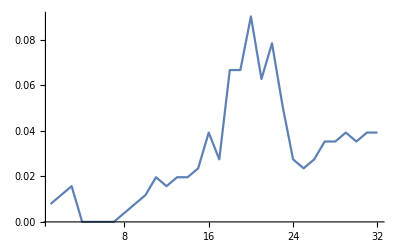
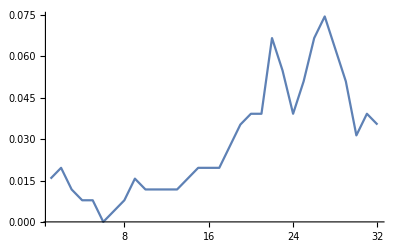
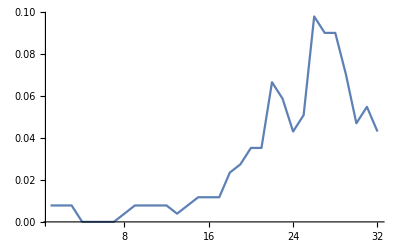
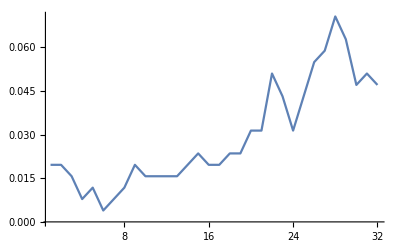

```mathematica
tfs=Import[#,"XML"]&/@tffiles;
rgbas=ReadTF/@tfs;
ListLinePlot[#[[All,4]],PlotRange->All,PlotLegends->Automatic]&/@rgbas
```

```mathematica
WriteTF[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xmlobject},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xmlobject=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function created using Wolfram Mathematica"]},VoreenData,{}];
Export[filename,xmlobject, "XML"]
(*rgbafunction2*)
]
```

```mathematica
CreateColorFunction[peaks_]:=Module[{a2,rgba2,intensity2,rgbafunction2},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & )(* for return only. not used in this function *)
]
```

```mathematica
intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
(*If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];*)
(*index0=Flatten@Position[alpha0,_?(#>0&)];*)
index0=rangeOfAlpha[[2;;-2]]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33}

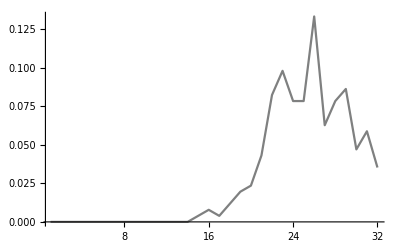
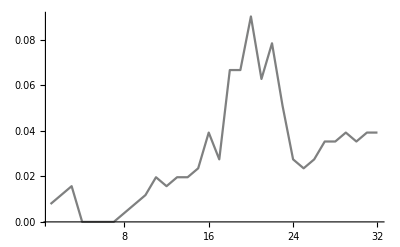
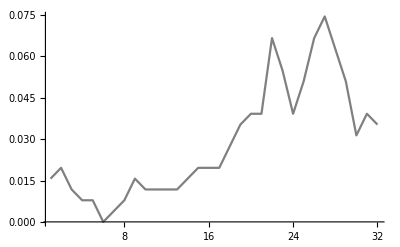
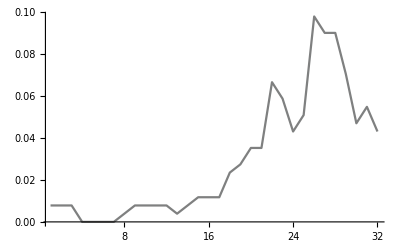
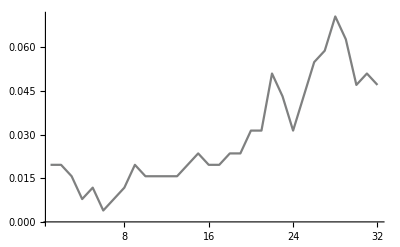

```mathematica
colors=Table[CreateColorFunction[rgbas[[i]][[All,4]]],{i,Length@rgbas}];
Table[ListLinePlot[rgbas[[i]][[All,4]],PlotRange->All,PlotLegends->Automatic,ColorFunction->colors[[i]]],{i,Length@rgbas}]
```

```mathematica
(*path3=FileNameJoin[{path,"tf"}];
If[!DirectoryQ[path3],CreateDirectory[path3]];
Table[WriteTF[rgbas[[i]][[All,4]],FileNameJoin[{path3,tfifilenames[[i]]}]],{i,Length@rgbas}];*)
```

```mathematica
pyfile=FileNameJoin[{path,"_voreen_render_with_transfer_functions_in_directory.py"}];
list=StringSplit[Import[pyfile],"\n"];
list2=If[StringContainsQ[#,"mypath="],"mypath="<>ToString@InputForm@path,#]&/@list;
Export[pyfile,list2,"List"];
```